```mathematica
<<MaTeX`
ℏSI=1.054571817*10^-10;"N*nm*fs";
hEV=4.135667731;"eV*fs";
ℏEV=hEV/(2π);
cUA=299.792458; "nm/fs";
qSI=1.602176565*10^-19;"Coulombs";
ℏcUA=ℏEV*cUA; "eV*nm";
ℏcSI=ℏSI*cUA;"N*(nm)^2";
αEF=0.0072973525693;
(*10 eV/nm = 1.602176565 nN*)
(*ColorFunction->(ColorData["SunsetColors"][1-#]&)*)
```

```mathematica
UF=(ℏEV*αEF)/cUA*(1.602176565/10)(*factor a multiplicar para obtener 2.5669*10^-6 nN en la fuerza*)
```

2.56697×10^-6

```mathematica
valors[t_,T_,N_]:=N/2(t/T+1)-1;
valors[0.6,50,2^19]
```

265289.

Gráficas  para a = 1 nm, b = 3 nm

```mathematica
dataX1=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/FFTW/Graficas_preliminares/recoil_force_x_dipolar_aprox_results_1_4.txt","Table"];
dataZ1=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/FFTW/Graficas_preliminares/recoil_force_z_dipolar_aprox_results_1_4.txt","Table"];
dataX2=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/FFTW/Graficas_preliminares/recoil_force_x_dipolar_aprox_results_4_7.txt","Table"];
dataZ2=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/FFTW/Graficas_preliminares/recoil_force_z_dipolar_aprox_results_4_7.txt","Table"];
dataX3=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/FFTW/Graficas_preliminares/recoil_force_x_dipolar_aprox_results_7_99.txt","Table"];
dataZ3=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/FFTW/Graficas_preliminares/recoil_force_z_dipolar_aprox_results_7_99.txt","Table"];
```

```mathematica
LegendLabel->Underscript[MaTeX["\\frac{c}{\\hbar\\alpha}F^\\text{ret}_{l=1,x}(t)",FontSize->20], MaTeX["\\text{[fs$^{-2}$]}",FontSize->20]]
```

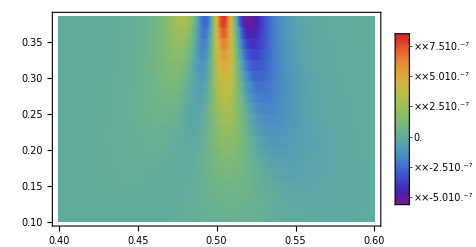

```mathematica
Parte1X=ListDensityPlot[dataX1,ColorFunction->"Rainbow",AspectRatio->1/GoldenRatio,ColorFunctionScaling->True,PlotRange->{{0.4,0.6},All,All},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->70,LegendMargins->5,LabelStyle->Directive[ Black,FontFamily->"Latin Modern Math",FontSize->12]],Right],PlotRange->All,FrameLabel->{{MaTeX["\\beta",FontSize->12],None},{MaTeX["t\\,\\text{[fs]}",FontSize->12],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->12],TicksStyle->Directive[Black,Thickness[0.005]],FrameStyle->Directive[Black,Thickness[0.005]],ClippingStyle->Automatic]
```

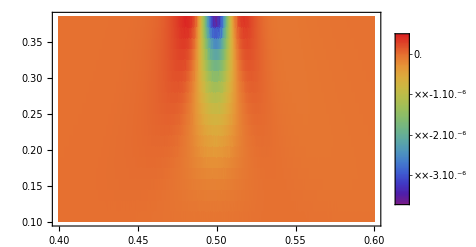

```mathematica
Parte1Z=ListDensityPlot[dataZ1,ColorFunction->"Rainbow",AspectRatio->1/GoldenRatio,ColorFunctionScaling->True,PlotRange->{{0.4,0.6},All,All},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->70,LegendMargins->5,LabelStyle->Directive[ Black,FontFamily->"Latin Modern Math",FontSize->12]],Right],PlotRange->All,FrameLabel->{{MaTeX["\\beta",FontSize->12],None},{MaTeX["t\\,\\text{[fs]}",FontSize->12],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->12],TicksStyle->Directive[Black,Thickness[0.005]],FrameStyle->Directive[Black,Thickness[0.005]],ClippingStyle->Automatic]
```

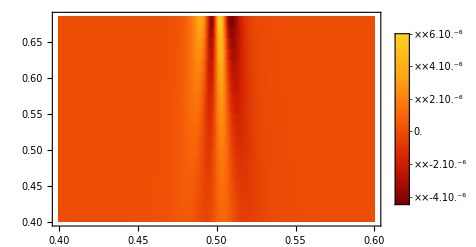

```mathematica
Parte2X=ListDensityPlot[dataX2,ColorFunction->"SolarColors",AspectRatio->1/GoldenRatio,ColorFunctionScaling->True,PlotRange->{{0.4,0.6},All,All},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->70,LegendMargins->5,LabelStyle->Directive[ Black,FontFamily->"Latin Modern Math",FontSize->12]],Right],PlotRange->All,FrameLabel->{{MaTeX["\\beta",FontSize->12],None},{MaTeX["t\\,\\text{[fs]}",FontSize->12],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->12],FrameStyle->Directive[Black,Thickness[0.005]],ClippingStyle->Automatic]
```

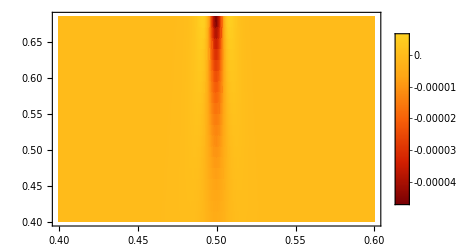

```mathematica
Parte2Z=ListDensityPlot[dataZ2,ColorFunction->"SolarColors",AspectRatio->1/GoldenRatio,ColorFunctionScaling->True,PlotRange->{{0.4,0.6},All,All},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->70,LegendMargins->5,LabelStyle->Directive[ Black,FontFamily->"Latin Modern Math",FontSize->12]],Right],PlotRange->All,FrameLabel->{{MaTeX["\\beta",FontSize->12],None},{MaTeX["t\\,\\text{[fs]}",FontSize->12],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->12],FrameStyle->Directive[Black,Thickness[0.005]],ClippingStyle->Automatic]
```

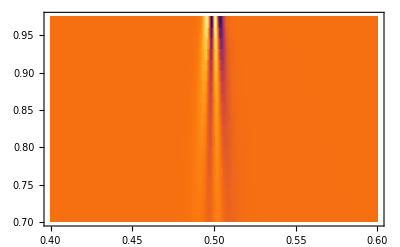

```mathematica
Parte3X=ListDensityPlot[dataX3,ColorFunction->"SunsetColors",AspectRatio->1/GoldenRatio,ColorFunctionScaling->True,PlotRange->{{0.4,0.6},All,All},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->MaTeX["\\frac{c}{\\hbar\\alpha}F^\\text{ret}_{l=1,x}",FontSize->18],LegendMarkerSize->70,LegendMargins->5,LabelStyle->Directive[ Black,FontFamily->"Latin Modern Math",FontSize->12]],Right],PlotRange->All,FrameLabel->{{MaTeX["\\beta",FontSize->12],None},{MaTeX["t\\,\\text{[fs]}",FontSize->12],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->12],TicksStyle->Directive[Black,Thickness[0.005]],FrameStyle->Directive[Black,Thickness[0.005]],ClippingStyle->Automatic]
```

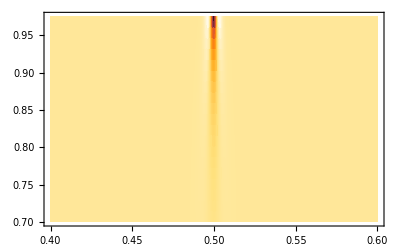

```mathematica
Parte3Z=ListDensityPlot[dataZ3,ColorFunction->"SunsetColors",AspectRatio->1/GoldenRatio,ColorFunctionScaling->True,PlotRange->{{0.4,0.6},All,All},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->MaTeX["\\frac{c}{\\hbar\\alpha}F^\\text{ret}_{l=1,z}",FontSize->18],LegendMarkerSize->70,LegendMargins->5,LabelStyle->Directive[ Black,FontFamily->"Latin Modern Math",FontSize->12]],Right],PlotRange->All,FrameLabel->{{MaTeX["\\beta",FontSize->12],None},{MaTeX["t\\,\\text{[fs]}",FontSize->12],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->12],TicksStyle->Directive[Black,Thickness[0.005]],FrameStyle->Directive[Black,Thickness[0.005]],ClippingStyle->Automatic]
```

```mathematica
Propuesta1=GraphicsColumn[{Parte3X,Parte2X,Parte1X},Left,-133]
```

-Graphics-

```mathematica
Propuesta2=GraphicsColumn[{Parte3Z,Parte2Z,Parte1Z},Left,-133]
```

-Graphics-

```mathematica
Export["x_parte_1.jpg",Parte1X,ImageResolution->200]
Export["z_parte_1.jpg",Parte1Z,ImageResolution->200]
Export["x_parte_2.jpg",Parte2X,ImageResolution->200]
Export["z_parte_2.jpg",Parte2Z,ImageResolution->200]
Export["x_parte_3.jpg",Parte3X,ImageResolution->200]
Export["z_parte_3.jpg",Parte3Z,ImageResolution->200]
```

x_parte_1.jpg

z_parte_1.jpg

x_parte_2.jpg

z_parte_2.jpg

x_parte_3.jpg

z_parte_3.jpg

```mathematica
Export["Propuesta_x_1_3.jpg",Propuesta1,ImageResolution->200];
Export["Propuesta_z_1_3.jpg",Propuesta2,ImageResolution->200];
```

Gráficas  para a = 10 nm, b = 12 nm

```mathematica
dataX1=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/FFTW/Graficas_preliminares/recoil_force_x_dipolar_aprox_results_10_12_beta_1.txt","Table"];
dataZ1=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/FFTW/Graficas_preliminares/recoil_force_z_dipolar_aprox_results_10_12_beta_1.txt","Table"];
dataX2=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/FFTW/Graficas_preliminares/recoil_force_x_dipolar_aprox_results_10_12_beta_2.txt","Table"];
dataZ2=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/FFTW/Graficas_preliminares/recoil_force_z_dipolar_aprox_results_10_12_beta_2.txt","Table"];
dataX3=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/FFTW/Graficas_preliminares/recoil_force_x_dipolar_aprox_results_10_12_beta_3.txt","Table"];
dataZ3=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/FFTW/Graficas_preliminares/recoil_force_z_dipolar_aprox_results_10_12_beta_3.txt","Table"];
```

```mathematica
Parte1compX1012=ListDensityPlot[dataX1,ColorFunction->"Rainbow",AspectRatio->1/GoldenRatio,ColorFunctionScaling->True,PlotRange->{All,All,All},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->70,LegendMargins->5,LabelStyle->Directive[ Black,FontFamily->"Latin Modern Math",FontSize->12]],Right],PlotRange->All,FrameLabel->{{MaTeX["\\beta",FontSize->12],None},{MaTeX["t\\,\\text{[fs]}",FontSize->12],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->12],TicksStyle->Directive[Black,Thickness[0.005]],FrameStyle->Directive[Black,Thickness[0.005]],ClippingStyle->Automatic]
```

-Graphics-

```mathematica
Parte1compZ1012=ListDensityPlot[dataZ1,ColorFunction->"Rainbow",AspectRatio->1/GoldenRatio,ColorFunctionScaling->True,PlotRange->{All,All,All},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->70,LegendMargins->5,LabelStyle->Directive[ Black,FontFamily->"Latin Modern Math",FontSize->12]],Right],PlotRange->All,FrameLabel->{{MaTeX["\\beta",FontSize->12],None},{MaTeX["t\\,\\text{[fs]}",FontSize->12],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->12],TicksStyle->Directive[Black,Thickness[0.005]],FrameStyle->Directive[Black,Thickness[0.005]],ClippingStyle->Automatic]
```

-Graphics-

```mathematica
Parte2compX1012=ListDensityPlot[dataX2,ColorFunction->"SolarColors",AspectRatio->1/GoldenRatio,ColorFunctionScaling->True,PlotRange->{All,All,All},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->70,LegendMargins->5,LabelStyle->Directive[ Black,FontFamily->"Latin Modern Math",FontSize->12]],Right],PlotRange->All,FrameLabel->{{MaTeX["\\beta",FontSize->12],None},{MaTeX["t\\,\\text{[fs]}",FontSize->12],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->12],FrameStyle->Directive[Black,Thickness[0.005]],ClippingStyle->Automatic]
```

-Graphics-

```mathematica
Parte2compZ1012=ListDensityPlot[dataZ2,ColorFunction->"SolarColors",AspectRatio->1/GoldenRatio,ColorFunctionScaling->True,PlotRange->{All,All,All},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->70,LegendMargins->5,LabelStyle->Directive[ Black,FontFamily->"Latin Modern Math",FontSize->12]],Right],PlotRange->All,FrameLabel->{{MaTeX["\\beta",FontSize->12],None},{MaTeX["t\\,\\text{[fs]}",FontSize->12],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->12],FrameStyle->Directive[Black,Thickness[0.005]],ClippingStyle->Automatic]
```

-Graphics-

```mathematica
Parte3compX1012=ListDensityPlot[dataX3,ColorFunction->"SunsetColors",AspectRatio->1/GoldenRatio,ColorFunctionScaling->True,PlotRange->{All,All,All},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->MaTeX["\\frac{c}{\\hbar\\alpha}F^\\text{ret}_{l=1,x}",FontSize->18],LegendMarkerSize->70,LegendMargins->5,LabelStyle->Directive[ Black,FontFamily->"Latin Modern Math",FontSize->12]],Right],PlotRange->All,FrameLabel->{{MaTeX["\\beta",FontSize->12],None},{MaTeX["t\\,\\text{[fs]}",FontSize->12],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->12],TicksStyle->Directive[Black,Thickness[0.005]],FrameStyle->Directive[Black,Thickness[0.005]],ClippingStyle->Automatic]
```

-Graphics-

```mathematica
Parte3compZ1012=ListDensityPlot[dataZ3,ColorFunction->"SunsetColors",AspectRatio->1/GoldenRatio,ColorFunctionScaling->True,PlotRange->{All,All,All},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->MaTeX["\\frac{c}{\\hbar\\alpha}F^\\text{ret}_{l=1,z}",FontSize->18],LegendMarkerSize->70,LegendMargins->5,LabelStyle->Directive[ Black,FontFamily->"Latin Modern Math",FontSize->12]],Right],PlotRange->All,FrameLabel->{{MaTeX["\\beta",FontSize->12],None},{MaTeX["t\\,\\text{[fs]}",FontSize->12],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->12],TicksStyle->Directive[Black,Thickness[0.005]],FrameStyle->Directive[Black,Thickness[0.005]],ClippingStyle->Automatic]
```

-Graphics-

```mathematica
PropuestaX1012=GraphicsColumn[{Parte3compX1012,Parte2compX1012,Parte1compX1012},Left,-133]
PropuestaZ1012=GraphicsColumn[{Parte3compZ1012,Parte2compZ1012,Parte1compZ1012},Left,-133]
```

-Graphics-

-Graphics-

```mathematica
Export["Propuesta_x_10_12.jpg",PropuestaX1012,ImageResolution->200];
Export["Propuesta_z_10_12.jpg",PropuestaZ1012,ImageResolution->200];
```

```mathematica
dataX=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/FFTW/recoil_force_x_dipolar_aprox_results.txt","Table"];
dataZ=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/FFTW/recoil_force_z_dipolar_aprox_results.txt","Table"];
```

```mathematica
Dimensions[dataX]
```

{183500,3}

```mathematica
Parte0X=ListDensityPlot[dataX,ColorFunction->"SunsetColors",ColorFunctionScaling->True,PlotRange->{All,All,All},PlotLegends->BarLegend[Automatic,LegendMarkerSize->300,LegendMargins->5,LegendLabel->Underscript[MaTeX["\\frac{c}{\\hbar\\alpha}F^\\text{ret}_{l=1,x}(t)",FontSize->20], MaTeX["\\text{[fs$^{-2}$]}",FontSize->20]],LabelStyle->Directive[ Black,FontFamily->"Latin Modern Math",FontSize->20]],PlotRange->All,FrameLabel->{{MaTeX["\\beta",FontSize->20],None},{MaTeX["t\\,\\text{[fs]}",FontSize->18],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->20],TicksStyle->Directive[Black,Thickness[0.005]],FrameStyle->Directive[Black,Thickness[0.005]],ClippingStyle->Automatic]
```

-Graphics-

```mathematica
Parte0Z=ListDensityPlot[dataZ,ColorFunction->ColorData["SunsetColors"],ColorFunctionScaling->True,PlotRange->{All,All,All},PlotLegends->BarLegend[Automatic,LegendMarkerSize->300,LegendMargins->5,LegendLabel->Underscript[MaTeX["\\frac{c}{\\hbar\\alpha}F^\\text{ret}_{l=1,z}(t)",FontSize->20], MaTeX["\\text{[fs$^{-2}$]}",FontSize->20]],LabelStyle->Directive[ Black,FontFamily->"Latin Modern Math",FontSize->20]],PlotRange->All,FrameLabel->{{MaTeX["\\beta",FontSize->20],None},{MaTeX["t\\,\\text{[fs]}",FontSize->18],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->20],TicksStyle->Directive[Black,Thickness[0.005]],FrameStyle->Directive[Black,Thickness[0.005]],ClippingStyle->Automatic]
```

-Graphics-

```mathematica
ListPlot3D[dataZ,ColorFunction->ColorData["SunsetColors"],BoxRatios->{1, 1, 1},ColorFunctionScaling->True,PlotRange->{All,All,All},PlotLegends->BarLegend[Automatic,LegendMarkerSize->300,LegendMargins->5,LegendLabel->Underscript[MaTeX["\\frac{c}{\\hbar\\alpha}F^\\text{ret}_{l=1,z}(t)",FontSize->20], MaTeX["\\text{[fs$^{-2}$]}",FontSize->20]],LabelStyle->Directive[ Black,FontFamily->"Latin Modern Math",FontSize->20]],PlotRange->All,AxesLabel->{MaTeX["t\\,\\text{[fs]}",FontSize->18],MaTeX["\\beta",FontSize->20]},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->20],TicksStyle->Directive[Black,Thickness[0.005]],ClippingStyle->Automatic]
```

-Graphics3D-